```mathematica
opencldirectory="/home/chris/Programming/GPU/opencl3/";
```

## Helper

```mathematica
NotebookEvaluate[opencldirectory<>"DetectPeriodTools2.wl"]
NotebookEvaluate[opencldirectory<>"build.wl"]
```

```mathematica
GPUStructureSearch[{20, {2, 1}, 2}]
```

{151,187,189,221,635,889,15903}

#### Utility

```mathematica
Clear[ProgressMap]
ProgressMap[f_, l_List]:=Module[{stdout=PrintTemporary[""], len=Length[l], begin=TimeObject[], cur, avg,eta, tmp},
Table[
tmp=f[l[[i]]];
NotebookDelete[stdout];
cur=TimeObject[];avg=(cur-begin)/i;eta=begin+len*avg;stdout=PrintTemporary["Step "<>ToString[i]<>"/"<>ToString[len]<>" ("<>ToString[N[100*i/len]]<>"% complete, Avg Time "<>ToString[QuantityMagnitude[avg,"Seconds"]]<>" seconds per elem, ETA "<>DateString[eta, "DateTimeShort"]<>")"]; 
tmp, {i, len}]]
ProgressMap[f_, l_Integer]:=ProgressMap[f, ConstantArray[0, l]]
```

#### Rule Generation

```mathematica
Clear[GoodRuleCondition, GoodTotalisticRuleCondition, RandomGoodRules, RandomGoodTotalisticRules];

GoodRuleCondition[ K_, R_][rule_]:=If[Length[Last[CellularAutomaton[{rule, K, R},{RandomInteger[K-1,100],0},100]]]>150,False,With[{l=Join[Table[Length[StripZeros[CellularAutomaton[{rule,K, R},{RandomInteger[K-1,100],0},{{{100}}}]]],10], Table[Length[StripZeros[CellularAutomaton[{rule, K, R},{RandomInteger[K-1,20],0},{{{100}}}]]],10]]},Mean[l]<100&&Min[l]==0&&Max[l]>0]];

GoodTotalisticRuleCondition[ K_, R_][rule_]:=If[Length[Last[CellularAutomaton[{rule, {K, 1}, R},{RandomInteger[K-1,100],0},100]]]>150,False,With[{l=Join[Table[Length[StripZeros[CellularAutomaton[{rule, {K, 1}, R},{RandomInteger[K-1,100],0},{{{100}}}]]],10], Table[Length[StripZeros[CellularAutomaton[{rule, {K, 1}, R},{RandomInteger[K-1,20],0},{{{100}}}]]],20]]},Mean[l]<100&&Min[l]==0&&Max[l]>0]];

RandomGoodRules[n_, K_:2, R_:1]:={#, K, R}&/@ParallelSelect[Union@ParallelTable[rca[{K,R},"Quiescent"->True,"Type"->"Symmetric"]["RuleNumber"], n], GoodRuleCondition[K, R]]

RandomGoodTotalisticRules[n_, K_:2, R_:1]:={#, {K, 1}, R}&/@ParallelSelect[Union@ParallelTable[rca[{K,R},"Quiescent"->True,"Type"->"Totalistic"]["TotalisticCode"], n], GoodTotalisticRuleCondition[K, R]]
```

#### Checking and Cleanup

```mathematica
Clear[DedupRuleAndRes]
DedupRuleAndRes[{rule_, res_}]:={rule, SortBy[DedupSame[Join@@ParallelMap[init|->DetectPeriod[rule, init], res]], "Canonical"]}
```

```mathematica
Clear[NonTrivialMetric];
NonTrivialMetric[{rule_, res_}]:=Which[
Length[res]==1&&res[[1, "Canonical"]]<16, False, 
AnyTrue[res, KeyExistsQ[#, "IsGliderGun"]&&#["IsGliderGun"]&], True,
Length[res]>40, False,
True, True
]

Clear[NonTrivialMetricRaw];
NonTrivialMetricRaw[{rule_, res_}]:=Which[
Length[res]==1&&res[[1]]<16, False, 
Length[res]>20, False,
True, True
]
```

#### Visualization

```mathematica
FixInteresting[]:=(interestingRules=Union[interestingRules]; interestingResults=(Last@*Sort)/@Values[GroupBy[interestingResults, First]])
ResetInteresting[]:=(interestingRules={};interestingResults={};)

ResetInteresting[]
```

```mathematica
Clear[DecentRunLength]
DecentRunLength[res_, default_]:=Round@Min[If[KeyExistsQ[res, "Period"], 2.2* res["Period"]+30, default], 500]

Clear[DecentRunLengthRaw];
DecentRunLengthRaw[rule_, res_, default_]:=Round@Min[With[{k=AnalyzeRule[rule]["Colors"]},{p=Length[FindRepeatDeterministicByStripZeros[CellularAutomaton[rule, {IntegerDigits[res, k], 0}, default]]]}, If[p!=0, 2.2*p+30, default]], 500]
```

```mathematica
Clear[DisplayRuleResult, DisplayRuleResultRaw]

DisplayRuleResult[rule_, results_, resultSteps_:200, maxNum_:50]:=With[
{k=AnalyzeRule[rule]["Colors"]},Pane[{
Button["Add", AppendTo[interestingRules, rule]; AppendTo[interestingResults, {rule, results}]],
Labeled[ArrayPlot[CellularAutomaton[rule, {RandomInteger[{0, k-1}, 100], 0}, 100]],ClickToCopy[rule]], Row[Table[
Labeled[ArrayPlot[CellularAutomaton[rule, {IntegerDigits[init["Canonical"], k], 0}, DecentRunLength[init, resultSteps]]], ClickToCopy[init["Canonical"], init]]
, {init, results[[;;UpTo[maxNum]]]}], Spacer[1]]
}, 100000]]

DisplayRuleResultRaw[rule_, results_, resultSteps_:200, maxNum_:50]:=With[
{k=AnalyzeRule[rule]["Colors"]},Pane[{
Button["Add", AppendTo[interestingRules, rule]; AppendTo[interestingResults, {rule, results}]],
Labeled[ArrayPlot[CellularAutomaton[rule, {RandomInteger[{0, k-1}, 100], 0}, 100]],ClickToCopy[rule]], Row[Table[
Labeled[ArrayPlot[CellularAutomaton[rule, {IntegerDigits[init, k], 0}, DecentRunLengthRaw[rule, init, resultSteps]]], ClickToCopy[init]]
, {init, results[[;;UpTo[maxNum]]]}], Spacer[1]]
}, 100000]]
```

```mathematica
Clear[DisplayRuleResults]

(* resultdisplayoffset=1;
DisplayRuleResults[ress_, raw_:True, numToShow_:50,resultSteps_:200, maxNum_:50]:=(resultdisplayoffset=1;FixInteresting[];Dynamic[Column[Join[
ParallelTable[
If[raw, DisplayRuleResultRaw, DisplayRuleResult][ress[[i, 1]], ress[[i, 2]], resultSteps, maxNum], {i, resultdisplayoffset, Min[resultdisplayoffset+numToShow-1, Length[ress]]}
], 
If[
resultdisplayoffset+numToShow<Length[ress], {{
"Too many results to show, so they have been truncated.", Button["See More",resultdisplayoffset+=numToShow]
}}, {{"You've seen all results. ", Button["Close", resultdisplayoffset=Length[ress]+1; NotebookDelete[EvaluationCell[]]]}}]]], None, TrackedSymbols:>{resultdisplayoffset}]) *)

DisplayRuleResults[ress_, raw_:True, numToShow_:50,resultSteps_:200, maxNum_:50]:=(FixInteresting[];Column[
ParallelTable[If[raw, DisplayRuleResultRaw, DisplayRuleResult][i[[1]], i[[2]], resultSteps, maxNum], {i, ress}]])
```

```mathematica
VisualizeInterestingResults[steps_:100]:=Column@ParallelTable[DisplayRuleResult@@i, {i, interestingResults}]
```

```mathematica
Clear[VisualizeSingleResult];
VisualizeSingleResult[rule_List, init_List, steps_Integer:100,ops:OptionsPattern[ArrayPlot]]:=ArrayPlot[RunCA[rule, init, steps], {ops}]

VisualizeSingleResult[rule_List, init_Integer, steps_Integer:100,ops:OptionsPattern[ArrayPlot]]:=VisualizeSingleResult[rule, IntegerDigits[init, AnalyzeRule[rule]["Colors"]], steps, {ops}]

VisualizeSingleResult[init_Association, steps_Integer:100,ops:OptionsPattern[ArrayPlot]]:=VisualizeSingleResult[init["Rule"], init["Original"], steps, {ops}]
```

#### Running

```mathematica
Clear[FullStructureSearchRaw, FullStructureSearch];
FullStructureSearchRaw[rules_, min_:0, max_:1000000, timeout_:1000]:=Module[
{ress,nontrivial},
FixInteresting[];

(* Prep memoization in a parallel manner *)
ParallelMap[AnalyzeRule, rules];

ress=ProgressMap[rule|->{rule, GPUStructureSearch[rule, min, max, timeout]}, rules];
ress=Select[ress, ListQ@*Last];
Print[Length[ress]," rules searched with results: ",Iconize[ress]];

nontrivial=ParallelSelect[ress, NonTrivialMetricRaw];
If[Length[nontrivial]<10, nontrivial=ress];
Print[Length[nontrivial], " nontrivial results: ", Iconize[nontrivial]];

DisplayRuleResults[nontrivial]
]

FullStructureSearch[rules_, min_:0, max_:1000000, timeout_:1000]:=Module[
{ress, ressDeduped, nontrivial},
FixInteresting[];

(* Prep memoization in a parallel manner *)
ParallelMap[AnalyzeRule, rules];

ress=ProgressMap[rule|->{rule, GPUStructureSearch[rule, min, max, timeout]}, rules];
ress=Select[ress, ListQ@*Last];
Print[Length[ress]," rules searched with results: ",Iconize[ress]];

(* ressDeduped=ParallelSelect[ress, Length[Last[#]]<50&]; *);
ressDeduped=Function[{rule, res}, If[Length[res]<100, {rule, res}, {rule,Union[Sort[ Join[res[[;;50]], RandomChoice[res, 50]]]]}]]@@@ress;

ressDeduped=Map[DedupRuleAndRes, ressDeduped];
Print[Total[Length/@ress], " total results deduped to ",Total[Length/@ressDeduped], " ", Iconize[ressDeduped]];

nontrivial=ParallelSelect[ressDeduped, NonTrivialMetric];
If[Length[nontrivial]<10, nontrivial=ressDeduped];
Print[Length[nontrivial], " nontrivial results: ", Iconize[nontrivial]];

 nontrivial=ressDeduped;

DisplayRuleResults[nontrivial, False]
]

FullStructureSearchQuiet[rules_, min_:0, max_:1000000, timeout_:1000]:=Module[
{ress, ressDeduped, nontrivial},
FixInteresting[];

(* Prep memoization in a parallel manner *)
ParallelMap[AnalyzeRule, rules];

ress=ProgressMap[rule|->{rule, GPUStructureSearch[rule, min, max, timeout]}, rules];
ress=Select[ress, ListQ@*Last];

ressDeduped=Map[DedupRuleAndRes, ress];

ressDeduped
]
```

## Other

```mathematica
Clear[MaxTotalisticRule]
MaxTotalisticRule[k_, r_]:=(k^((k-1)(2r+1)+1)-1)
```

```mathematica
Clear[QuiescentQ]
QuiescentQ[rule_]:=AnalyzeRule[rule]["Quiescent"]
```

```mathematica
Clear[ThereExistsInitWhichDoesntGrowInfinitelyOrDie]
ThereExistsInitWhichDoesntGrowInfinitelyOrDie[rule_, numChecks_:100]:=AnyTrue[Range[numChecks],seed|->(SeedRandom[seed];With[{
l=Length[StripZeros[
RunCA[rule, RandomInteger[k^40], {{{50}}}]
]]},
l>0&&l<40
])]
```

```mathematica
Clear[AttemptDedup]
AttemptDedup[rule_, inits_, timeout_:30]:=TimeConstrained[DedupSame[SortBy[Join@@ParallelMap[DetectPeriod[rule, #]&, inits], #Original&]][[All, "Original"]], timeout, inits]
```

## Example

```mathematica
k=2;r=1;
rules={#, {k, 1}, r}&/@Range[MaxTotalisticRule[k, r]];
rules=ParallelSelect[rules, QuiescentQ];
Row[ClickToCopy[AArrayPlot[#, RandomInteger[2^20], 20], #]&/@rules]
```

-Graphics-{2,{2,1},1}-Graphics-{4,{2,1},1}-Graphics-{6,{2,1},1}-Graphics-{8,{2,1},1}-Graphics-{10,{2,1},1}-Graphics-{12,{2,1},1}-Graphics-{14,{2,1},1}

```mathematica
rules=ParallelSelect[rules, ThereExistsInitWhichDoesntGrowInfinitelyOrDie];
Row[ClickToCopy[AArrayPlot[#, RandomInteger[2^20], 20], #]&/@rules, Spacer[2]]
```

-Graphics-{4,{2,1},1}-Graphics-{12,{2,1},1}

```mathematica
res=ProgressMap[#->AttemptDedup[#, GPUStructureSearch[#, 0, 100000]]&,rules]
```

{{4,{2,1},1}→{3},{12,{2,1},1}→{3,7}}

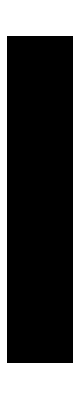
{{4,{2,1},1},-Graphics-3}
{{12,{2,1},1},-Graphics-3-Graphics-7}

{False,True,False,False,False,True,False}

```mathematica
Column[ParallelTable[With[{rule=i[[1]], inits=i[[2]]},  {ClickToCopy[rule],
Row[ClickToCopy[AArrayPlot[rule, #], #]&/@inits[[;;UpTo[100]]]],
If[Length[inits]>100, "...", Nothing]
}], {i, res}]]
```

## k=2, r=1

```mathematica
k=2;r=1;
rules={#, {k, 1}, r}&/@Range[MaxTotalisticRule[k, r]];
rules=ParallelSelect[rules, QuiescentQ];
rules=ParallelSelect[rules, ThereExistsInitWhichDoesntGrowInfinitelyOrDie];
res=ProgressMap[#->AttemptDedup[#, GPUStructureSearch[#, 0, 1000000]]&,rules];
```

```mathematica
Column[ParallelTable[With[{rule=i[[1]], inits=i[[2]]},  {ClickToCopy[rule],
Row[ClickToCopy[AArrayPlot[rule, #], #]&/@inits[[;;UpTo[100]]]],
If[Length[inits]>100, "...", Nothing]
}], {i, res}]]
```

{{4,{2,1},1},-Graphics-3}
{{12,{2,1},1},-Graphics-3-Graphics-7}

{False,True,False,False,False,True,False}

## k=2, r=2

```mathematica
k=2;r=2;
rules={#, {k, 1}, r}&/@Range[MaxTotalisticRule[k, r]];
rules=ParallelSelect[rules, QuiescentQ];
rules=ParallelSelect[rules, ThereExistsInitWhichDoesntGrowInfinitelyOrDie];
res=ProgressMap[#->AttemptDedup[#, GPUStructureSearch[#, 0, 1000000]]&,rules];
```

```mathematica
Column[ParallelTable[With[{rule=i[[1]], inits=i[[2]]},  {ClickToCopy[rule],
If[Length[inits]>20, "(Not Showing All)", Nothing],
Row[ClickToCopy[AArrayPlot[rule, #], #]&/@inits[[;;UpTo[20]]]]
}], {i, res}]]
```

{{8,{2,1},2},-Graphics-7}
{{20,{2,1},2},-Graphics-189-Graphics-635-Graphics-151-Graphics-187-Graphics-195}
{{24,{2,1},2},-Graphics-7-Graphics-15}
{{40,{2,1},2},-Graphics-7}
{{52,{2,1},2},(Not Showing All),-Graphics-55-Graphics-59-Graphics-195-Graphics-667-Graphics-1243-Graphics-1373-Graphics-1659-Graphics-1779-Graphics-18487-Graphics-37611-Graphics-42107-Graphics-42507-Graphics-42635-Graphics-42695-Graphics-44437-Graphics-44587-Graphics-44895-Graphics-56477-Graphics-56669-Graphics-56869}
{{56,{2,1},2},-Graphics-7-Graphics-15-Graphics-31}

{False,True,False,False,False,True,False}

## k=2, r=3

```mathematica
k=2;r=3;
rules={#, {k, 1}, r}&/@Range[MaxTotalisticRule[k, r]];
rules=ParallelSelect[rules, QuiescentQ];
rules=ParallelSelect[rules, ThereExistsInitWhichDoesntGrowInfinitelyOrDie];
```

```mathematica
Iconize[rules]
```

```mathematica
res=ProgressMap[#->AttemptDedup[#, GPUStructureSearch[#, 0, 1000000]]&,rules];
```

```mathematica
Column[ParallelTable[With[{rule=i[[1]], inits=i[[2]]},  {ClickToCopy[rule],
If[Length[inits]>20, "(Not Showing All)", Nothing],
Row[ClickToCopy[AArrayPlot[rule, #], #]&/@inits[[;;UpTo[20]]]]
}], {i, res}]]
```

{{8,{2,1},3},-Graphics-39}
{{16,{2,1},3},-Graphics-15}
{{24,{2,1},3},-Graphics-207-Graphics-7}
{{40,{2,1},3},-Graphics-39-Graphics-107-Graphics-159-Graphics-501039-Graphics-7335-Graphics-45453}
{{48,{2,1},3},-Graphics-15-Graphics-31}
{{72,{2,1},3},-Graphics-39-Graphics-63}
{{80,{2,1},3},-Graphics-15}
{{88,{2,1},3},(Not Showing All),-Graphics-7-Graphics-11-Graphics-13-Graphics-15-Graphics-23-Graphics-29-Graphics-30-Graphics-39-Graphics-45-Graphics-46-Graphics-57-Graphics-58-Graphics-60-Graphics-63-Graphics-126-Graphics-183-Graphics-207-Graphics-219-Graphics-223-Graphics-231}
{{100,{2,1},3},-Graphics-191-Graphics-765-Graphics-1399-Graphics-1023-Graphics-693}
{{104,{2,1},3},-Graphics-39-Graphics-107-Graphics-63-Graphics-119-Graphics-447-Graphics-513375-Graphics-3831}
{{112,{2,1},3},-Graphics-15-Graphics-31-Graphics-63}
{{136,{2,1},3},-Graphics-39}
{{144,{2,1},3},-Graphics-15}
{{152,{2,1},3},-Graphics-207-Graphics-47-Graphics-255-Graphics-7}
{{164,{2,1},3},-Graphics-1273-Graphics-38743-Graphics-55323-Graphics-20611}
{{168,{2,1},3},-Graphics-39-Graphics-107-Graphics-159-Graphics-450943-Graphics-501039-Graphics-7335-Graphics-45453}
{{176,{2,1},3},-Graphics-15-Graphics-31}
{{200,{2,1},3},-Graphics-39-Graphics-63}
{{208,{2,1},3},-Graphics-15}
{{216,{2,1},3},(Not Showing All),-Graphics-7-Graphics-11-Graphics-13-Graphics-15-Graphics-23-Graphics-29-Graphics-30-Graphics-39-Graphics-45-Graphics-46-Graphics-47-Graphics-55-Graphics-57-Graphics-58-Graphics-59-Graphics-60-Graphics-61-Graphics-63-Graphics-79-Graphics-87}
{{228,{2,1},3},(Not Showing All),-Graphics-47-Graphics-255-Graphics-511-Graphics-1023-Graphics-1161-Graphics-195-Graphics-27-Graphics-771-Graphics-8771-Graphics-12415-Graphics-2571-Graphics-363-Graphics-5557-Graphics-12363-Graphics-171-Graphics-13851-Graphics-27163-Graphics-47755-Graphics-73867-Graphics-83995}
{{232,{2,1},3},-Graphics-181963-Graphics-183947-Graphics-39-Graphics-107-Graphics-63-Graphics-119-Graphics-255-Graphics-479-Graphics-231-Graphics-807-Graphics-1831-Graphics-513375-Graphics-726239-Graphics-924127-Graphics-5671-Graphics-13415-Graphics-45983-Graphics-45191-Graphics-108103-Graphics-156455}
{{240,{2,1},3},-Graphics-15-Graphics-31-Graphics-63-Graphics-127}

{False,True,False,False,False,True,False}

## k=2, r=4

```mathematica
k=2;r=4;
rules={#, {k, 1}, r}&/@Range[MaxTotalisticRule[k, r]];
rules=ParallelSelect[rules, QuiescentQ];
rules=ParallelSelect[rules, ThereExistsInitWhichDoesntGrowInfinitelyOrDie];
Iconize[rules]
```

```mathematica
res=ProgressMap[#->AttemptDedup[#, GPUStructureSearch[#, 0, 10000]]&,rules];
Iconize[res]
```

```mathematica
Column[ParallelTable[With[{rule=i[[1]], inits=i[[2]]},  {ClickToCopy[rule],
If[Length[inits]>20, "(Not Showing All)", Nothing],
Row[ClickToCopy[AArrayPlot[rule, #], #]&/@inits[[;;UpTo[20]]]]
}], {i, res}]]
```

{{32,{2,1},4},-Graphics-31}
{{36,{2,1},4},}
{{40,{2,1},4},-Graphics-799-Graphics-47-Graphics-7335}
{{48,{2,1},4},-Graphics-159}
{{68,{2,1},4},-Graphics-9201-Graphics-5}
{{72,{2,1},4},-Graphics-4303-Graphics-103}
{{96,{2,1},4},-Graphics-31-Graphics-63}
{{100,{2,1},4},-Graphics-795}
{{104,{2,1},4},(Not Showing All),-Graphics-7-Graphics-11-Graphics-13-Graphics-14-Graphics-19-Graphics-21-Graphics-22-Graphics-25-Graphics-26-Graphics-28-Graphics-31-Graphics-39-Graphics-44-Graphics-47-Graphics-52-Graphics-55-Graphics-56-Graphics-57-Graphics-59-Graphics-61}
{{112,{2,1},4},-Graphics-831-Graphics-23-Graphics-15}
{{152,{2,1},4},-Graphics-5757-Graphics-7047}
{{160,{2,1},4},-Graphics-31}
{{164,{2,1},4},(Not Showing All),-Graphics-3-Graphics-5-Graphics-6-Graphics-9-Graphics-10-Graphics-11-Graphics-12-Graphics-13-Graphics-17-Graphics-18-Graphics-20-Graphics-21-Graphics-22-Graphics-24-Graphics-26-Graphics-27-Graphics-31-Graphics-35-Graphics-36-Graphics-37}
{{168,{2,1},4},-Graphics-7-Graphics-167-Graphics-479-Graphics-1967-Graphics-7335}
{{176,{2,1},4},-Graphics-159-Graphics-383-Graphics-23-Graphics-951-Graphics-1663}
{{196,{2,1},4},-Graphics-639-Graphics-5113}
{{200,{2,1},4},-Graphics-639-Graphics-1663-Graphics-4303-Graphics-3711-Graphics-1831}
{{208,{2,1},4},-Graphics-219-Graphics-127-Graphics-639}
{{224,{2,1},4},-Graphics-31-Graphics-63-Graphics-127}
{{228,{2,1},4},-Graphics-959-Graphics-1023-Graphics-819-Graphics-5}
{{232,{2,1},4},-Graphics-5461-Graphics-2891}
{{288,{2,1},4},-Graphics-31}
{{292,{2,1},4},(Not Showing All),-Graphics-3-Graphics-6-Graphics-9-Graphics-12-Graphics-18-Graphics-24-Graphics-36-Graphics-48-Graphics-63-Graphics-96-Graphics-126-Graphics-155-Graphics-192-Graphics-195-Graphics-217-Graphics-239-Graphics-247-Graphics-252-Graphics-255-Graphics-299}
{{296,{2,1},4},-Graphics-767-Graphics-47-Graphics-7335}
{{304,{2,1},4},-Graphics-159-Graphics-255}
{{324,{2,1},4},(Not Showing All),-Graphics-3-Graphics-5-Graphics-6-Graphics-10-Graphics-11-Graphics-12-Graphics-13-Graphics-20-Graphics-22-Graphics-24-Graphics-26-Graphics-40-Graphics-44-Graphics-48-Graphics-52-Graphics-55-Graphics-59-Graphics-67-Graphics-80-Graphics-87}
{{328,{2,1},4},-Graphics-4303-Graphics-103}
{{352,{2,1},4},-Graphics-31-Graphics-63}
{{356,{2,1},4},-Graphics-1023-Graphics-2435-Graphics-171}
{{360,{2,1},4},(Not Showing All),-Graphics-7-Graphics-11-Graphics-13-Graphics-14-Graphics-19-Graphics-21-Graphics-22-Graphics-25-Graphics-26-Graphics-28-Graphics-31-Graphics-39-Graphics-44-Graphics-47-Graphics-52-Graphics-55-Graphics-56-Graphics-57-Graphics-59-Graphics-61}
{{368,{2,1},4},-Graphics-831-Graphics-15}
{{408,{2,1},4},-Graphics-6139-Graphics-5757-Graphics-7047-Graphics-767-Graphics-1455-Graphics-3711-Graphics-239}
{{416,{2,1},4},-Graphics-31}
{{420,{2,1},4},-Graphics-7055-Graphics-67}
{{424,{2,1},4},-Graphics-7-Graphics-167-Graphics-343-Graphics-943-Graphics-1511-Graphics-3359-Graphics-1967-Graphics-7335-Graphics-9753}
{{432,{2,1},4},-Graphics-159-Graphics-415-Graphics-23-Graphics-951-Graphics-767-Graphics-991-Graphics-1951-Graphics-2967-Graphics-255-Graphics-1535-Graphics-3071-Graphics-1487}
{{452,{2,1},4},-Graphics-3-Graphics-395-Graphics-3069-Graphics-1675}
{{456,{2,1},4},-Graphics-39-Graphics-767-Graphics-959-Graphics-1831-Graphics-4303-Graphics-5095-Graphics-153-Graphics-1855}
{{464,{2,1},4},-Graphics-219-Graphics-127-Graphics-255-Graphics-495-Graphics-975}
{{480,{2,1},4},-Graphics-31-Graphics-63-Graphics-127-Graphics-255}
{{544,{2,1},4},-Graphics-31}
{{548,{2,1},4},}
{{552,{2,1},4},-Graphics-799-Graphics-47-Graphics-7335}
{{560,{2,1},4},-Graphics-159}
{{580,{2,1},4},-Graphics-9201-Graphics-5-Graphics-239}
{{584,{2,1},4},-Graphics-311-Graphics-4303-Graphics-103}
{{608,{2,1},4},-Graphics-31-Graphics-63}
{{612,{2,1},4},-Graphics-887-Graphics-7855-Graphics-795-Graphics-17-Graphics-9}
{{616,{2,1},4},(Not Showing All),-Graphics-7-Graphics-14-Graphics-19-Graphics-21-Graphics-25-Graphics-28-Graphics-31-Graphics-55-Graphics-56-Graphics-59-Graphics-62-Graphics-77-Graphics-89-Graphics-107-Graphics-110-Graphics-112-Graphics-118-Graphics-124-Graphics-127-Graphics-154}
{{624,{2,1},4},-Graphics-831-Graphics-191-Graphics-1023-Graphics-375-Graphics-23-Graphics-15}
{{664,{2,1},4},(Not Showing All),-Graphics-191-Graphics-207-Graphics-223-Graphics-243-Graphics-251-Graphics-253-Graphics-335-Graphics-367-Graphics-371-Graphics-375-Graphics-382-Graphics-413-Graphics-414-Graphics-431-Graphics-439-Graphics-446-Graphics-475-Graphics-477-Graphics-485-Graphics-486}
{{672,{2,1},4},-Graphics-31}
{{676,{2,1},4},(Not Showing All),-Graphics-3-Graphics-6-Graphics-9-Graphics-11-Graphics-12-Graphics-13-Graphics-18-Graphics-22-Graphics-24-Graphics-26-Graphics-35-Graphics-36-Graphics-37-Graphics-41-Graphics-44-Graphics-47-Graphics-48-Graphics-49-Graphics-52-Graphics-61}
{{680,{2,1},4},-Graphics-7-Graphics-167-Graphics-479-Graphics-1967-Graphics-7335}
{{688,{2,1},4},-Graphics-159-Graphics-383-Graphics-23-Graphics-951-Graphics-1663-Graphics-511-Graphics-1487}
{{708,{2,1},4},-Graphics-639-Graphics-5113}
{{712,{2,1},4},-Graphics-639-Graphics-1663-Graphics-4303-Graphics-1855-Graphics-39-Graphics-3711-Graphics-3703}
{{720,{2,1},4},-Graphics-219-Graphics-127-Graphics-639}
{{736,{2,1},4},-Graphics-31-Graphics-63-Graphics-127}
{{744,{2,1},4},-Graphics-5461}
{{792,{2,1},4},-Graphics-15-Graphics-47-Graphics-819}
{{800,{2,1},4},-Graphics-31}
{{804,{2,1},4},-Graphics-1161-Graphics-3}
{{808,{2,1},4},-Graphics-383-Graphics-47-Graphics-7335}
{{816,{2,1},4},-Graphics-159-Graphics-255-Graphics-495}
{{836,{2,1},4},(Not Showing All),-Graphics-3-Graphics-5-Graphics-6-Graphics-10-Graphics-11-Graphics-12-Graphics-13-Graphics-20-Graphics-21-Graphics-22-Graphics-24-Graphics-26-Graphics-27-Graphics-40-Graphics-42-Graphics-43-Graphics-44-Graphics-48-Graphics-52-Graphics-53}
{{840,{2,1},4},-Graphics-4303-Graphics-103}
{{864,{2,1},4},-Graphics-31-Graphics-63}
{{868,{2,1},4},-Graphics-37-Graphics-41-Graphics-3251-Graphics-7051-Graphics-3013-Graphics-27-Graphics-5142-Graphics-2309-Graphics-2115-Graphics-2005-Graphics-3107-Graphics-1091-Graphics-3097-Graphics-1019}
{{872,{2,1},4},(Not Showing All),-Graphics-7-Graphics-11-Graphics-13-Graphics-14-Graphics-19-Graphics-21-Graphics-22-Graphics-25-Graphics-26-Graphics-28-Graphics-31-Graphics-39-Graphics-44-Graphics-47-Graphics-52-Graphics-55-Graphics-56-Graphics-57-Graphics-59-Graphics-61}
{{880,{2,1},4},-Graphics-3487-Graphics-3899-Graphics-831-Graphics-959-Graphics-191-Graphics-15-Graphics-383-Graphics-1391-Graphics-3511-Graphics-6015-Graphics-1487-Graphics-7935-Graphics-23}
{{920,{2,1},4},-Graphics-1007-Graphics-1227-Graphics-2005-Graphics-3058-Graphics-5031-Graphics-6103-Graphics-2047-Graphics-7032-Graphics-119-Graphics-1135-Graphics-1111-Graphics-5019-Graphics-7023-Graphics-6045-Graphics-7047-Graphics-1175-Graphics-111-Graphics-4071}
{{928,{2,1},4},-Graphics-31}
{{932,{2,1},4},-Graphics-7055-Graphics-67-Graphics-5-Graphics-195}
{{936,{2,1},4},-Graphics-189-Graphics-1003-Graphics-1015-Graphics-2007-Graphics-8013-Graphics-8029-Graphics-9019-Graphics-7-Graphics-167-Graphics-1197-Graphics-7004-Graphics-183-Graphics-179}
{{944,{2,1},4},-Graphics-159-Graphics-415-Graphics-23-Graphics-951-Graphics-495-Graphics-991-Graphics-2015-Graphics-2967-Graphics-1951-Graphics-1743-Graphics-3487-Graphics-1487-Graphics-1501-Graphics-255}
{{964,{2,1},4},-Graphics-3-Graphics-395-Graphics-1023-Graphics-2047-Graphics-4095-Graphics-4363-Graphics-8721-Graphics-21-Graphics-771-Graphics-27-Graphics-3075-Graphics-107-Graphics-4619-Graphics-8267-Graphics-3387-Graphics-1675-Graphics-6667}
{{968,{2,1},4},-Graphics-1855-Graphics-2023-Graphics-3703-Graphics-3815-Graphics-39-Graphics-311-Graphics-959-Graphics-1911-Graphics-3339-Graphics-5387-Graphics-4871-Graphics-847-Graphics-615-Graphics-7175-Graphics-153-Graphics-6439-Graphics-1831-Graphics-4303}
{{976,{2,1},4},-Graphics-219-Graphics-127-Graphics-255-Graphics-495-Graphics-975-Graphics-1983-Graphics-3903-Graphics-1935}
{{992,{2,1},4},-Graphics-31-Graphics-63-Graphics-127-Graphics-255-Graphics-511}

## Further Exploration

```mathematica
AttemptDedup[{88,{2,1},3}, GPUStructureSearch[{88,{2,1},3}, 0, 10000], 100]
```

{5063,6015,7283,8157,11,3579,1631,2875,7,6139}

```mathematica
AArrayPlot[{88,{2,1},3}, #, 300]&/@
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
AArrayPlot[{292,{2,1},4}, #, 500]&/@{155, 3}
```

{-Graphics-,-Graphics-}

```mathematica
AArrayPlot[{872,{2,1},4}, 7, 300]
```

-Graphics-

```mathematica
AArrayPlot[{676,{2,1},4}, 9, 1000]
```

-Graphics-

```mathematica
With[{rand=RandomInteger[{0, 1}, 100]}, {AArrayPlot[{408,{2,1},4}, Flatten[Transpose[{rand, rand}]], ImageSize->{Automatic, 200}], AArrayPlot[{20,{2,1},2},rand, ImageSize->{Automatic, 200}]}]
```

{-Graphics-,-Graphics-}

```mathematica
AttemptDedup[{408,{2,1},4}, GPUStructureSearch[{408,{2,1},4}, 0, 1000000000]]
```

{26611,53235,401359,802767,24895,49983,837572951871,1787,800895,53199,137313108991,268174335,17125543167}

```mathematica
AArrayPlot[{408,{2,1},4}, #]&/@
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}